```mathematica
Charting`$InteractiveHighlighting=False
```

False

```mathematica
n=9; (* Number of eigenstates *)
rMax=3; (* Size of the box *)
int[r_]:={r,0,rMax};
```

```mathematica
V[r_]:=Piecewise[{{0,Abs[r]<rMax},{∞,True}}];
```

```mathematica
{{efn1,evl1},{efn2,evl2}}=NDEigensystem[{-1/2 Laplacian[u[r],{r}]+# u[r],DirichletCondition[u[r]==0,True]},u[r],int[r],n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->10^-3}}}}]&/@{V[r],r^2}//Transpose;
```

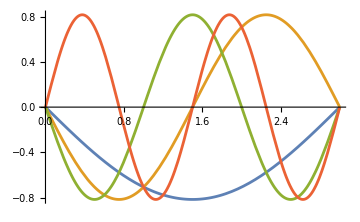
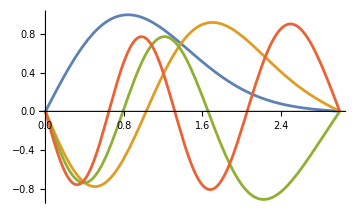

```mathematica
Plot[Take[#,4]//Evaluate,int[r],PlotRange->All,ImageSize->Medium]&/@{efn2,evl2}
```

```mathematica
Sort[#]&/@{efn1,evl1}//Column
```

{0.548311,2.19325,4.9348,8.77298,13.7078,19.7392,26.8673,35.0919,44.4132}
{2.12169,4.97382,8.07278,11.918,16.8133,22.8152,29.9239,38.1356,47.4478}

```mathematica
evalsSq=Abs[#]^2&/@evl2;
```

```mathematica
NIntegrate[#,int[r],PrecisionGoal->4]&/@evalsSq
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
If[OddQ[n],
list=2&/@Range[1,n-1];
AppendTo[list,1],
list=2&/@Range[1,n]
]
Length@list
```

{2,2,2,2,2,2,2,2,1}

9

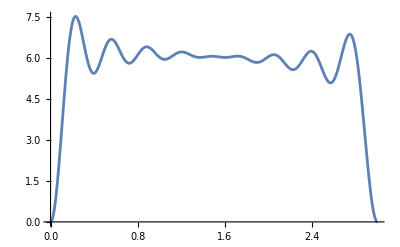

```mathematica
rho[l_]:=list.evalsSq/.{r->l};
Plot[rho[r],int[r],PlotRange->All]
```

```mathematica
ldaEn=-3/4(3/π)^(1/3)NIntegrate[rho[r]^(4/3),int[r],PrecisionGoal->4]
```

-22.7635

```mathematica
ldaPot=-(3/π)^(1/3)rho[r]^(1/3);
```

```mathematica
enHart=1/2 NIntegrate[(rho[r]rho[l])/Abs[r-l]^2,int[r],int[l],PrecisionGoal->3]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in r near {r,l} = {1.5,2.53237}. NIntegrate obtained 7.70662×10^8 and 1.12804×10^8 for the integral and error estimates.

3.85331×10^8

```mathematica
potHart=Integrate[rho[l]/(√((r-l)^2+ϵ)),int[r]];
```

```mathematica
(* Actual self-consistent loop for the Kohn-Sham equations *)
{evalKs,efnKs}=NDEigensystem[{-1/2 Laplacian[u[r],{r}]+(potHart[r]+ldaPot+r^2)u[r],DirichletCondition[u[r]==0,True]},u[r],int[r],n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->10^-3}}}}];
```

NDEigensystem::femcnsd: The PDE coefficient -r^2+(3/π)^(1/3) (2 Abs[«21»[«5»][«1»]]^2+2 («1»)^2+«5»+2 «1»+Abs[«1»]^2)^(1/3)-(∫_0^3 (2 Abs[«1»]^2+2 Abs[«1»]^2+2 Abs[«1»]^2+2 («1»)^2+2 («1»)^2+2 («1»)^2+2 Abs[«1»]^2+2 Abs[«1»]^2+Abs[InterpolatingFunction[«5»][«1»]]^2)/(√(Plus[«2»]^2+ϵ))ⅆr)[r] does not evaluate to a numeric scalar at the coordinate {1.5}; it evaluated to -0.454459-(∫_0^3 (2 Abs[«1»]^2+2 Abs[«1»]^2+2 Abs[«1»]^2+«4»+2 Abs[«1»]^2+Abs[InterpolatingFunction[«5»][«1»]]^2)/(√(Plus[«2»]^2+ϵ))ⅆ1.5)[1.5] instead.

General::stop: Further output of NDEigensystem::femcnsd will be suppressed during this calculation.

Set::shape: Lists {evalKs,efnKs} and NDEigensystem[{u[r] (r^2-Times[«2»]^(1/3) Plus[«9»]^(1/3)+(∫_0^3 Power[«2»] Plus[«9»]ⅆr)[r])-u''[r]/2,DirichletCondition[u[r]==0,True]},u[r],{r,0,3},9,Method→{SpatialDiscretization→{FiniteElement,{MeshOptions→{«1»}}}}] are not the same shape.

$Aborted

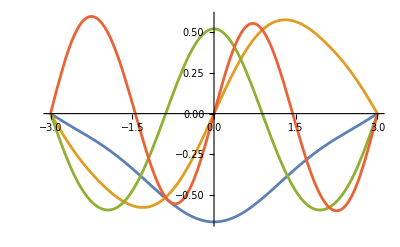

```mathematica
Plot[Take[efnKs,4]//Evaluate,int[r],PlotRange->All]
```

```mathematica
Min[evalKs]
```

17.3663